## HMQC-TOCSY covariance processing

```mathematica
SetDirectory[NotebookDirectory[] <> "/.."]
```

/Users/mu3q/GitHub/NMRprocess2

```mathematica
Needs["NMRProcess2`"]
```

## Load data

```mathematica
rawfid= ReadBruker["ExampleData/glucose-361/19/ser"]
```

-|NMR..1--

Only the raw NMR acquisition data is loaded, without any information about dwell time, etc. The time domain structure must be set explicitly:

```mathematica
hmqcfid=SetTimeDomain[rawfid,{512,512}]
```

-|NMR..2--

In order to obtain calibrated plots, we need to set the spectral width (in ppm) and the offsets:

```mathematica
hmqcfid=SetProp[hmqcfid,{Offset->{4.41,88.4},SpectralWidth->{12,190}}];
```

## Fourier Transform

```mathematica
spect=StatesFFT2[hmqcfid,Phase2->10,Phase1->90,SI1->2048,SI2->1024]
```

-|NMR..2--

## Plots

A full 2D spectrum can be plotted with NMRContourPlot.

The contour levels are automatically set to 10%, 20%, ... of the highest point in the spectrum.
In the present case, we are only interested in a subregion of the spectrum. Crop[]  can be used to reduce the
data:

```mathematica
overview=Crop[spect,{{6.,2.},{105.,55.}}]
```

-|NMR..2--

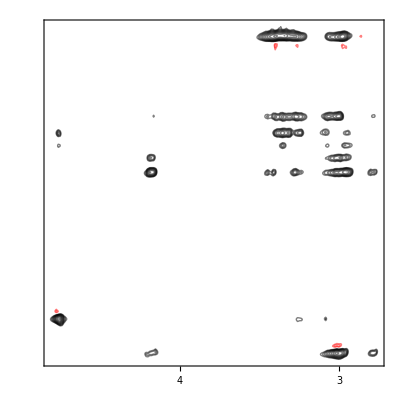

```mathematica
Show[NMRContourPlot[overview,Gain->0.9],NMRContourPlot[overview,Gain->-1,ContourStyle->Red]]
```

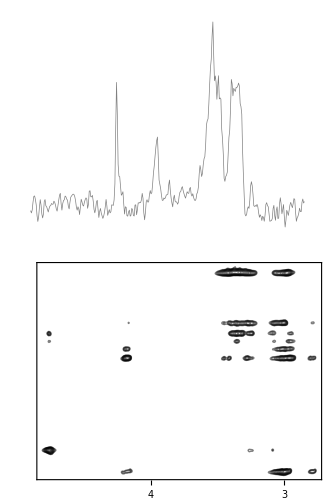

```mathematica
NMRContourProjectionPlot[overview,Gain->0.9]
```

```mathematica
covTOCSY=CovHSQCTOCSY[overview]
```

-|NMR..2--

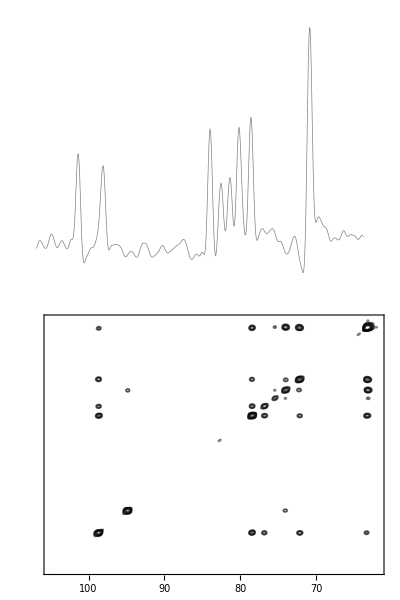

-Graphics-

```mathematica
NMRContourProjectionPlot[covTOCSY,Gain->1.5]
```

```mathematica
covTOCSY[Offset]
```

{80.004,80.004}

```mathematica
covTOCSY[SpectralWidth]
```

{50.0049,50.0049}

```mathematica
covTOCSY[SpectSize]
```

{540,540}

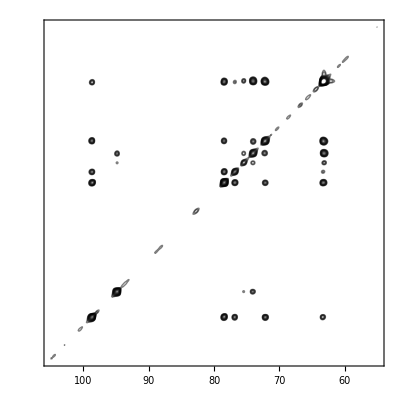

```mathematica
NMRContourPlot[covTOCSY,Gain->2]
```

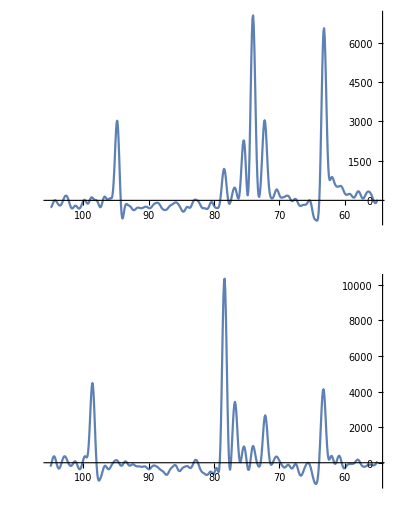

```mathematica
GraphicsGrid[Transpose[{PlotNMR1D[ExtractRow[covTOCSY,{74.0,78.22}],PlotRange->All]}]]
```

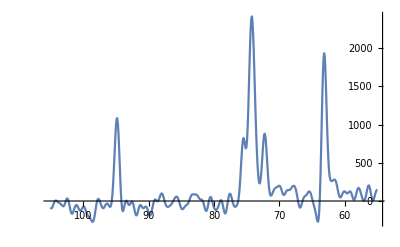

```mathematica
PlotNMR1D[ExtractRow[covTOCSY,74.5],PlotRange->All]
```